```mathematica
mult={10./45.,9./45.,8./45.,7./45.,6./45.,5./45.};
exact[x_,y_]:=Block[{r,th,res,i},
r=Norm[{x,y}];
If[r>0,th=ArcTan[x,y],th=0];
If[th<0,th+=2Pi];
res = Sum[mult[[i]]Cos[i 2/3th]r^(i 2/3),{i,1,Length[mult]}];
res
]
```

-Graphics3D-

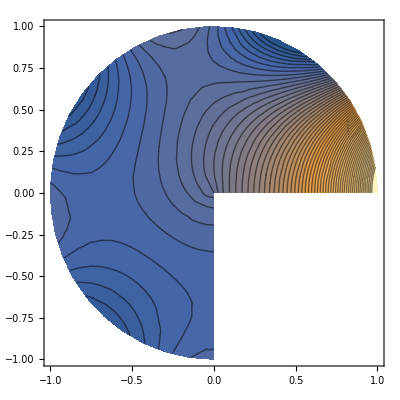

```mathematica
Plot3D[exact[x,y],{x,y}∈Disk[{0,0},1,{0,3Pi/2}],PlotRange->All]
ContourPlot[exact[x,y],{x,y}∈Disk[{0,0},1,{0,3Pi/2}],PlotRange->All,Contours->60]
```